## Hexi—PS14—2025 - 03 - 25

### Exercises from EIWL3 Section 35

```mathematica
Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

```mathematica
Select[Table[Interpreter["University"]["U of " <>X],{X,CharacterRange["A","Z"]}],Head[#]=!=Failure&]
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

```mathematica
Select[Interpreter["Movie"]/@CommonName/@EntityClass["AdministrativeDivision","AllUSStatesPlusDC"][EntityProperty["AdministrativeDivision","CapitalCity"]],Head[#]=!=Failure&]
```

{Phoenix,Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

```mathematica
Select[Interpreter["City"][StringJoin/@Permutations[{"a","i","l","m"}]],Head[#]=!=Failure&]
```

{Alim,Amli,Balm,Ilam,Lami,Lima,Lamai,Mali,Milah,Mali}

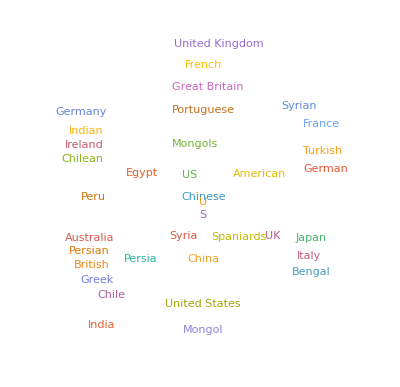

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
TextCases["She sells seashells by the sea shore","Noun"]
```

{seashells,sea,shore}

```mathematica
Length/@Values[TextCases[StringTake[WikipediaData["computers"],1000],{"Noun","Verb","Adjective"}]]
```

{54,23,20}

```mathematica
TextStructure[Take[TextSentences[WikipediaData["computers"]],1]]
```

{    A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence}

{    A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence}

```mathematica
Keys[TakeLargest[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]],10]]
```

{Rabbit,door,voice,time,way,Mouse,moment,thing,head,table}

```mathematica
CommunityGraphPlot[First[TextStructure[TextSentences[WikipediaData["language"]],"DependencyGraphs"]]]
```

CommunityGraphPlot::graph: A graph object is expected at position 1 in ….

CommunityGraphPlot[{-Graphics-}]

```mathematica
Length[WordList[#]]&/@{"Noun","Verb","Adjective","Adverb"}
```

{24493,6503,11392,3120}

```mathematica
WordTranslation[#,"French"]&/@IntegerName[Range[2,10]]//Flatten
```

{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}

### Exercises from EIWL3 Section 36

```mathematica
CloudPublish[Delayed[Style[RandomInteger[1000],1000]]]
```

CloudObject[https://www.wolframcloud.com/obj/896bbe64-1cf8-4bf8-b9c2-6899c78d9345]

```mathematica
CloudPublish[FormFunction[{"x"->"Number"},#x^#x&]]
```

CloudObject[https://www.wolframcloud.com/obj/5118b8c8-80b0-49f9-838e-ab81a2a3ae27]

```mathematica
CloudPublish[FormFunction[{"x"->"Number","y"->"Number"},#x^#y&]]
```

CloudObject[https://www.wolframcloud.com/obj/aff9bcbc-4218-4fe8-9f6e-c5ab1b89dfc8]

```mathematica
CloudPublish[FormFunction[{"topic"->"String"},WordCloud[WikipediaData[#topic]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/f312dff2-f31c-484e-a386-7234857e404d]

```mathematica
CloudPublish[FormFunction[{"String"->"String"},Style[StringReverse[#String],50]&]]
```

CloudObject[https://www.wolframcloud.com/obj/e6bfcd0e-8b2c-4c8d-9184-1a9ffa8fd2bc]

```mathematica
CloudPublish[FormPage[{"n"->"Integer"},Graphics[{RandomColor[],RegularPolygon[#n]}]&]]
```

CloudObject[https://www.wolframcloud.com/obj/43aae6fb-de4b-46ec-895b-2402988e4341]

```mathematica
CloudPublish[FormPage[{"location"->"Location","n"->"Number"},GeoListPlot[Nearest[EntityList["Volcano"],#location,#n]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/cd3c2ab6-979e-4646-a168-0229756ea1f3]